# BBP | 1. Baseline

## 00: Pre-Load

This part of the file is purely technical and serves to define folders, dates and default (figure) layouts

```mathematica
ClearAll["Global`*"];
```

```mathematica
CloudSave[EvaluationNotebook[]]
```

Save::sym: Argument EvaluationNotebook[] at position 2 is expected to be a symbol.

CloudObject[https://www.wolframcloud.com/obj/a3363565-bdb7-4455-8e25-6342c89447c5]

```mathematica
dir=NotebookDirectory[];
dirbu=NotebookDirectory[]<>"/_backup/";
Off[Syntax::stresc]
```

Autosave and backup

```mathematica
FileName=FileNameSplit[NotebookFileName[]][[-1]];
```

```mathematica
TimeStamp=ToString[Round[AbsoluteTime[]]];
```

```mathematica
SpecialNote="BU";
```

```mathematica
NotebookSave[EvaluationNotebook[],FileNameJoin[{dirbu,StringDelete[FileName,".nb"]<>" "<>TimeStamp<>" "<>SpecialNote<>".nb"}]]
```

```mathematica
NotebookSave[EvaluationNotebook[],FileNameJoin[{dir,FileName}]]
```

“Evaluate Above” shortcut

```mathematica
CreatePalette[Button["Evaluate Above",With[{nbI=InputNotebook[]},Do[SelectionMove[Experimental`FromCellIndex[nbI,i],All,Cell];
If[TextString["Style"/.Developer`CellInformation[nbI][[1]]]==="Input",SelectionEvaluateCreateCell[nbI]];,{i,1,Experimental`ToCellIndex@SelectedCells[nbI][[1]]}]],Method->"Queued"]];
```

Copy/Paste Output to Overleaf PGFPLOTS

```mathematica
VEC0=Function[out,StringReplace[ToString[NumberForm[out,4]],{"{"->"(","}"->")","},{"->")(","), ("->")("}]];
VEC=Function[out,StringReplace[VEC0[out],"), ("->")("]];
```

## 0: Preliminaries

### 0.0 Working Precision

```mathematica
Qp=MachinePrecision;
Ε=N[10^-(Qp-2),Qp];
```

### 0.1 Model Selection

```mathematica
Ui=1;"Utility = "<>{"CARA","Epstein-Zin"}[[Ui]]
Ϟi=1;"Payoff Distribution = "<>{"Gaussian","N/A","Binomial"}[[Ϟi]]
ϖi=1;"Public Info = "<>{"Bond + Stock","Stock only","Bond only","None"}[[ϖi]]
ι=False;"Initial Cons ="ι
Ϝ=True;"Production ="Ϝ
```

Utility = CARA

Payoff Distribution = Gaussian

Public Info = Bond + Stock

Initial Cons = False

Production = True

### 0.2 Preferences

```mathematica
β=0.95;
γ=4;
ψ=1;
```

```mathematica
If[And[γ==1/ψ,Ui==2],Ui=3;Style["Utility to CRRA",Yellow]]
If[And[γ==1,Ui==3],Ui=4;Style["Utility to Log",Yellow]]
If[And[Not[ι],Ui==2],ι=True;Style["Ini Cons to True",Yellow]]
If[And[γ==1,Ui==2],γ=1.000001;Style["γ to 1.000001",White]]
If[And[ψ==1,Ui==2],ψ=1.000001;Style["ψ to 1.000001",White]]
```

### 0.3 Model-Implied Settings

Preferences (U)

```mathematica
Piecewise[{{U[c_]:=-(1/γ)*Exp[-γ*c],Ui==1},{U[c_]:=c^(1-γ)/(1-γ),Ui==3},{U[c_]:=Log[c],Ui==4}}];
```

Learning (ϖ)

```mathematica
Piecewise[{{ϖ[x_,y_,z_]:=x,ϖi==1},{ϖ[x_,y_,z_]:=y,ϖi==2},{ϖ[x_,y_,z_]:=z,ϖi==3},{ϖ[x_,y_,z_]:=1,ϖi==4}}];
```

### 0.4 Distributional Parameters

```mathematica
CORR=0;
```

Production Parameters

```mathematica
c=5.;
K1 = 1.;
δ= 0.;
```

```mathematica
If[Not[Ϝ],δ=0.; K1 = 1.;]
```

Initial Endowment: Cash and Cash Equivalents

```mathematica
e0=1.5;
X0=0.;
Y0=0.;
```

Initial Endowment: Fraction of Random Supply

```mathematica
X0θ=0;
Y0θ=0;
```

Payoff Distribution

```mathematica
EΠ=1.;
SΠ=0.4;
```

Initial Payoff

```mathematica
Π0=EΠ;
C0=0;
```

Aggregate Supply

```mathematica
θXbar=1;
θYbar=1+Ε;
```

Noise Trader Demand Distribution

```mathematica
EθX=0.;
EθY=0.;
```

```mathematica
SθX=0.2;
SθY=(1/10)//N;
```

Bond Noise Trader weight on dollar noise

```mathematica
w$=0.0;
```

Private Signal (Highest level of τϵi will be picked in output graphs)

```mathematica
Ξτϵi=Table[ii,{ii,0.1,1.,(1.-0.1)/9}]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

Endogenous Distributional parameters

```mathematica
Nτϵi=Length[Ξτϵi];
τϵ0=Max[Ξτϵi];
```

```mathematica
σϵi=Sqrt[1/τϵi];
```

```mathematica
If[Ϟi==3,ρ=1/2 (1+√(τϵi/(4+τϵi)))];
```

```mathematica
μΠ=If[Ϟi==2,Log[EΠ^2/(√(SΠ^2+EΠ^2))],EΠ]
σΠ=If[Ϟi==2,Sqrt[Log[SΠ^2/EΠ^2+1]],SΠ]
```

1.

0.4

```mathematica
μθX=EθX
σθX=SθX
```

0.

0.2

```mathematica
μθY=EθY
σθY=SθY
```

0.

0.1

```mathematica
Β=1/(1+β);
```

### 0.7 Grid

Select here the numerical parameters:
-Nσπ and NσS determine the number of standard deviations on which the conjectured payoff and signal are defined
-Nπ and NS determine the number of points of the  conjectured payoff and signal grid

```mathematica
If[Not[Ϟi==3],
Nσπ=21;NNσπ=1;
Nπ=2*Nσπ*NNσπ+1,
Nπ=2;]
```

43

```mathematica
If[Not[Ϟi==3],
NσΠ=2;NNσΠ=1;
NΠ=2*NσΠ*NNσΠ+1,
NΠ=2;]
```

5

```mathematica
If[Not[Ϟi==3],If[Not[Mod[NNσπ,NNσΠ]==0],Style["ERROR! Please ensure NNσπ is a multiple of NNσΠ",Red]]]
```

Grid is symmetric in θY shocks

```mathematica
NθX=7;
NθY=7;
NσθX=2;
NσθY=2;
```

Set Midpoints etc.

```mathematica
If[Not[Ϟi==3],
NS=Nπ;
μSi=μΠi;
μπi=(Nπ+1)/2;
μΠi=(NΠ+1)/2;
σϵi=1/Sqrt[τϵi];,
NS=2;]
```

```mathematica
μθXi=(NθX+1)/2;
μθYi=(NθY+1)/2;
```

```mathematica
NN=NθX*NθY*NΠ
```

245

## 1: Variables and Distributions

### 1.1 Notation

Rational agent  holdings:

```mathematica
Do[X[Si]=Symbol["X"<>"S"<>ToString[Si]],{Si,NS}];
Do[C1[Si]=Symbol["C1"<>"S"<>ToString[Si]],{Si,NS}];
```

Rational agent conjectured aggregate holdings:

```mathematica
Do[XΣ[πi]=Symbol["XΣ"<>"π"<>ToString[πi]],{πi,Nπ}];
Do[YΣ[πi]=Symbol["YΣ"<>"π"<>ToString[πi]],{πi,Nπ}];
```

### 1.2 Conjectured Payoffs

```mathematica
ππ=μΠ+σΠ*Table[ii,{ii,-Nσπ,Nσπ,2*Nσπ/(Nπ-1)}];
πω=PDF[NormalDistribution[μΠ,σΠ]];
πΩ=SetPrecision[πω@ππ/Total[πω@ππ],Qp];
```

```mathematica
If[Ϟi==3,ππ={μΠ-σΠ,μΠ+σΠ};πω=Function[π,0*π+1/2];πΩ={1/2,1/2}];
```

### 1.3 Signals

```mathematica
S=ππ;
```

```mathematica
ψϵω=Function[{τϵi,ϵi},PDF[NormalDistribution[0,σϵi]][ϵi]];
```

```mathematica
Sω=Table[PDF[NormalDistribution[ππ[[πi]],σϵi]],{πi,Nπ}];
SΩπ=Table[Sω[[πi]][S]/Total[Sω[[πi]][S]],{πi,Nπ}]//N;
```

```mathematica
If[Ϟi==3,SΩπ={{ρ,1-ρ},{1-ρ,ρ}};Clear[Sω];ψϵω=Function[{τϵi,ϵi},Evaluate[DiscreteDelta[ϵi]*ρ+(1-DiscreteDelta[ϵi])*(1-ρ)]]];
```

```mathematica
χSΩπ=Compile[τϵi,Evaluate[SΩπ]];
```

### 1.4 Noise Trader Demand

```mathematica
θXω=PDF[NormalDistribution[μθX,σθX]];
```

```mathematica
θYω=PDF[NormalDistribution[μθY+w$*(1/PY),σθY]];
```

```mathematica
θXYω=Function[{x,y},Evaluate[PDF[MultinormalDistribution[{μθX,μθY+w$*(1/PY)},{{σθX^2,σθX*σθY*CORR},{σθX*σθY*CORR,σθY^2}}],{x,y}]]]
```

Function[{x,y},7.95775 ⅇ^(1/2 (-(0.+x) (0.+25. (0.+x))-(0.+y) (0.+100. (0.+y))))]

```mathematica
θXYωω=Function[{x,y},Evaluate[PDF[MultinormalDistribution[{μθX,μθY},{{σθX^2,σθX*σθY*CORR},{σθX*σθY*CORR,σθY^2}}],{x,y}]]]
```

Function[{x,y},7.95775 ⅇ^(1/2 (-(0.+x) (0.+25. (0.+x))-(0.+y) (0.+100. (0.+y))))]

### 1.5 State Variables

Grid (NB: ΞΠ must lie on the ππ grid)

```mathematica
If[Ϟi==3,ΞΠ=ππ;ΞΠi={1,2};,
ΞΠ=μΠ+σΠ*Table[ii,{ii,-NσΠ,NσΠ,2*NσΠ/(NΠ-1)}];
ΞΠi=Table[Sum[If[ππ[[πi]]===ΞΠ[[Πi]],πi,0],{πi,Nπ}],{Πi,NΠ}]]
```

{20,21,22,23,24}

```mathematica
ΞθX=μθX+σθX*Table[ii,{ii,-NσθX,NσθX,2*NσθX/(NθX-1)}];
ΞθY=μθY+σθY*Table[ii,{ii,-NσθY,NσθY,2*NσθY/(NθY-1)}];
```

```mathematica
ΞθXY=Table[{ΞθX[[ii]],ΞθY[[jj]]},{ii,NθX},{jj,NθY}];
```

Normalized density

```mathematica
ΞΠΩ=Simplify[πω@ΞΠ/Total[πω@ΞΠ]];
```

```mathematica
ΞθXΩ=SetPrecision[Simplify[θXω@ΞθX/Total[θXω@ΞθX]],Qp];
```

```mathematica
ΞθXYΩ=SetPrecision[Simplify[Table[θXYωω@@ΞθXY[[ii,jj]],{ii,NθX},{jj,NθY}]/Total[Total[Table[θXYωω@@ΞθXY[[ii,jj]],{ii,NθX},{jj,NθY}]]]],Qp];
```

Probability of state grid points

```mathematica
ΞΠXnYnΩ=Table[ΞΠΩ[[Πi]]*ΞθXYΩ[[θXi,θYi]],{Πi,NΠ},{θXi,NθX},{θYi,NθY}]//Simplify;
```

```mathematica
ΞΠXnYnΩ//Total//Total//Total//Simplify
```

1.

Midpoints and count

```mathematica
θXi0=(NθX+1)/2;
θYi0=(NθY+1)/2;
If[Not[Ϟi==3],Πi0=(NΠ+1)/2];
NθX*NθY*NΠ
```

245

Quick Grid Functions

```mathematica
Θ={θX,θY};
RΘ=Table[{θX->ΞθX[[θXi]],θY->ΞθY[[θYi]]},{θXi,NθX},{θYi,NθY}];
```

### 1.6 System Variables

```mathematica
Υ=DeleteCases[Flatten[{Table[X[Si],{Si,NS}],Table[C1[Si],{Si,NS}],Table[XΣ[πi],{πi,Nπ}],Table[YΣ[πi],{πi,Nπ}],{PX,PY,Ι}}],Null];
NΥ=Length[Flatten[Υ]];
```

### 1.7 All Variables

The second argument takes the place of Πi and only serves as a placeholder.

```mathematica
χΥΥ[τϵi_,∅_,Θ_,Υ_?VectorQ]:=Flatten[{τϵi,∅,Θ,Υ}]
```

```mathematica
ΥΥ=Flatten[{τϵi,∅,Θ,Υ}]
```

{τϵi,∅,θX,θY,XS1,XS2,XS3,XS4,XS5,XS6,XS7,XS8,XS9,XS10,XS11,XS12,XS13,XS14,XS15,XS16,XS17,XS18,XS19,XS20,XS21,XS22,XS23,XS24,XS25,XS26,XS27,XS28,XS29,XS30,XS31,XS32,XS33,XS34,XS35,XS36,XS37,XS38,XS39,XS40,XS41,XS42,XS43,C1S1,C1S2,C1S3,C1S4,C1S5,C1S6,C1S7,C1S8,C1S9,C1S10,C1S11,C1S12,C1S13,C1S14,C1S15,C1S16,C1S17,C1S18,C1S19,C1S20,C1S21,C1S22,C1S23,C1S24,C1S25,C1S26,C1S27,C1S28,C1S29,C1S30,C1S31,C1S32,C1S33,C1S34,C1S35,C1S36,C1S37,C1S38,C1S39,C1S40,C1S41,C1S42,C1S43,XΣπ1,XΣπ2,XΣπ3,XΣπ4,XΣπ5,XΣπ6,XΣπ7,XΣπ8,XΣπ9,XΣπ10,XΣπ11,XΣπ12,XΣπ13,XΣπ14,XΣπ15,XΣπ16,XΣπ17,XΣπ18,XΣπ19,XΣπ20,XΣπ21,XΣπ22,XΣπ23,XΣπ24,XΣπ25,XΣπ26,XΣπ27,XΣπ28,XΣπ29,XΣπ30,XΣπ31,XΣπ32,XΣπ33,XΣπ34,XΣπ35,XΣπ36,XΣπ37,XΣπ38,XΣπ39,XΣπ40,XΣπ41,XΣπ42,XΣπ43,YΣπ1,YΣπ2,YΣπ3,YΣπ4,YΣπ5,YΣπ6,YΣπ7,YΣπ8,YΣπ9,YΣπ10,YΣπ11,YΣπ12,YΣπ13,YΣπ14,YΣπ15,YΣπ16,YΣπ17,YΣπ18,YΣπ19,YΣπ20,YΣπ21,YΣπ22,YΣπ23,YΣπ24,YΣπ25,YΣπ26,YΣπ27,YΣπ28,YΣπ29,YΣπ30,YΣπ31,YΣπ32,YΣπ33,YΣπ34,YΣπ35,YΣπ36,YΣπ37,YΣπ38,YΣπ39,YΣπ40,YΣπ41,YΣπ42,YΣπ43,PX,PY,Ι}

```mathematica
NΥΥ=Length[Flatten[ΥΥ]]
```

179

## 2: Learning

### 2.1 Private Information (I)

```mathematica
ΞΩΩI=Table[πΩ[[πi]]*ψϵω[τϵi,S[[Si]]-ππ[[πi]]]*ϖ[θXYω[θXbar-XΣ[πi],θYbar-YΣ[πi]],θXω[θXbar-XΣ[πi]],θYω[θYbar-YΣ[πi]]],{πi,Nπ},{Si,NS}];
χΩΩI=Table[Compile[Evaluate[ΥΥ],Evaluate[ΞΩΩI[[;;,Si]]]],{Si,NS}];
```

```mathematica
RΩΩI=Flatten[Table[ΩΩI[πi,Si]->ΞΩΩI[[πi,Si]],{πi,Nπ},{Si,NS}]];
RΣΩI=Table[ΣΩI[Si]->Total[ΞΩΩI[[;;,Si]]],{Si,NS}];
```

### 2.2 Public Information (U)

```mathematica
ΞΩΩU=Table[πΩ[[πi]]*ϖ[θXYω[θXbar-XΣ[πi],θYbar-YΣ[πi]],θXω[θXbar-XΣ[πi]],θYω[θYbar-YΣ[πi]]],{πi,Nπ}];
χΩΩU=Compile[Evaluate[ΥΥ],Evaluate[ΞΩΩU[[;;]]]];
```

### 2.3 Private Signal Only (S)

```mathematica
ΞΩΩS=Table[πΩ[[πi]]*ψϵω[τϵi,S[[Si]]-ππ[[πi]]],{πi,Nπ},{Si,NS}];
χΩΩS=Table[Compile[Evaluate[ΥΥ],Evaluate[ΞΩΩS[[;;,Si]]]],{Si,NS}];
```

## 3: Production

### 3.1 Free Cash Flows

```mathematica
Δ1=Π0*(K1-Ι);
Δ2=ππ*(K1*(1- δ)+Ι)-(c*Ι^2)/(2*K1);
```

### 3.2 Optimal Production

```mathematica
LΙ=Δ1+((Δ2.ΞΩΩU)/Total[ΞΩΩU]);
```

```mathematica
FOCΙ=If[Ϝ,D[LΙ,Ι],Ι-0];
```

```mathematica
χFOCΙ=Compile[Evaluate[ΥΥ],Evaluate[FOCΙ],RuntimeOptions->{"EvaluateSymbolically"->False}];
```

## 4: Rational Traders

### 4.1 Initial Wealth

We assume agent’s initial endowment equals to the realization of residual stock supply. We assume agents cannot learn from their endowment. The assumption is taken to facilitate comparison with the closed form Rmodel.

```mathematica
W0=(X0+X0θ*θX)*(PX+Δ1)+(Y0+Y0θ*θY)*PY+e0
```

1.5

### 4.2 Budget Constraints

Solve for period-1 budget constraint to obtain bond holdings

```mathematica
Y[Si]=(W0-PX X[Si]-C1[Si])/PY;
```

Solve for period-2 budget constraint to obtain period-2 consumption:

```mathematica
Do[C2[πi,Si]=Y[Si]+X[Si]*Δ2[[πi]],{πi,Nπ}]
```

### 4.3 Lagrangian

```mathematica
L[Si]=If[ι,U[C1[Si]],0]+β*(Sum[ΩΩI[πi,Si]*U[C2[πi,Si]],{πi,Nπ}]/ΣΩI[Si]);
```

```mathematica
If[Ui==2,L[Si]=((1-Β)*C1[Si]^(1-ψ)+Β*(Sum[ΩΩI[πi,Si]*C2[πi,Si]^(1-γ),{πi,Nπ}]/ΣΩI[Si])^((1-ψ)/(1-γ)))^(1/(1-ψ))];
```

### 4.4 Optimality

```mathematica
FOCX[Si]=D[L[Si],X[Si]];
FOCC1[Si]=If[ι,D[L[Si],C1[Si]],C1[Si]-0];
```

```mathematica
ΞFOCX=Table[Evaluate[FOCX[Si]],{Si,NS}]/.RΩΩI/.RΣΩI;
ΞFOCC1=Table[Evaluate[FOCC1[Si]],{Si,NS}]/.RΩΩI/.RΣΩI;
```

```mathematica
χFOCX=Compile[Evaluate[ΥΥ],Evaluate[ΞFOCX],RuntimeOptions->{"EvaluateSymbolically"->False}];
χFOCC1=Compile[Evaluate[ΥΥ],Evaluate[ΞFOCC1],RuntimeOptions->{"EvaluateSymbolically"->False}];
```

## 5: Aggregate Quantities

### 5.1 Aggregate Stock Demand

```mathematica
ΞADX=Table[XΣ[πi]-Sum[SΩπ[[πi,Si]]*X[Si],{Si,NS}],{πi,Nπ}];
χADX=Compile[Evaluate[ΥΥ],Evaluate[ΞADX],RuntimeOptions->{"EvaluateSymbolically"->False}];
```

### 5.2 Aggregate Initial Wealth

Key learning assumption: Agents know random parts of endowment correspond to aggregate demand

```mathematica
Do[ΣW0[πi]=(X0+X0θ*XΣ[πi])*(PX+Δ1)+(Y0+Y0θ*YΣ[πi])*PY+e0,{πi,Nπ}];
```

```mathematica
If[ΣW0[1]==ΣW0[Nπ],ΣW00=ΣW0[1],Null];
```

### 5.3 Aggregate Bond Demand

We use the linearity of the market clearing condition to compute aggregate bond demand

```mathematica
ΞADY=Table[YΣ[πi]*PY-(ΣW0[πi]-PX*XΣ[πi]-Sum[SΩπ[[πi,Si]]*C1[Si],{Si,NS}]),{πi,Nπ}];
χADY=Compile[Evaluate[ΥΥ],Evaluate[ΞADY],RuntimeOptions->{"EvaluateSymbolically"->False}];
```

### 5.4 Market Clearing

```mathematica
Do[MCX[Πi]=XΣ[ΞΠi[[Πi]]]-(θXbar-θX),{Πi,NΠ}];
Do[MCY[Πi]=YΣ[ΞΠi[[Πi]]]-(θYbar-θY-w$*(1/PY)),{Πi,NΠ}];
```

```mathematica
Do[χMCX[Πi]=Compile[Evaluate[ΥΥ],Evaluate[MCX[Πi]],RuntimeOptions->{"EvaluateSymbolically"->False}],{Πi,NΠ}];
Do[χMCY[Πi]=Compile[Evaluate[ΥΥ],Evaluate[MCY[Πi]],RuntimeOptions->{"EvaluateSymbolically"->False}],{Πi,NΠ}];
```

### 5.5 Aggregate Initial Consumption

```mathematica
Do[ΣC1[Πi]=ΣW0[ΞΠi[[Πi]]]-PX*θX-PY*θY-w$*(1/PY),{Πi,NΠ}];
```

## 6: Zero Information Case (ξ)

### 6.1 Production

```mathematica
LΙξ=Δ1+((Δ2.πΩ)/Total[πΩ]);
```

```mathematica
FOCΙξ=If[Ϝ,D[LΙξ,Ι],Ι-0];
```

### 6.2 Initial Wealth

```mathematica
W0ξ=(X0+X0θ*θX)*(PXξ+Δ1)+(Y0+Y0θ*θY)*(PYξ+C0)+e0
```

1.5

### 6.3 Budget Constraints

Solve for period-1 budget constraint to obtain bond holdings

```mathematica
Yξ=(W0ξ-PXξ Xξ-C1ξ)/PYξ;
```

Solve for period-2 budget constraint to obtain period-2 consumption:

```mathematica
Do[C2ξ[πi]=Yξ+Xξ*Δ2[[πi]],{πi,Nπ}]
```

### 6.4 Lagrangian

```mathematica
Lξ=If[ι,U[C1ξ],0]+β*Sum[πΩ[[πi]]*U[C2ξ[πi]],{πi,Nπ}];
```

```mathematica
If[Ui==2,Lξ=((1-Β)*C1ξ^(1-ψ)+Β*(Sum[πΩ[[πi]]*C2ξ[πi]^(1-γ),{πi,Nπ}])^((1-ψ)/(1-γ)))^(1/(1-ψ))];
```

### 6.5 Optimality

```mathematica
FOCXξ=D[Lξ,Xξ];
FOCC1ξ=If[ι,D[Lξ,C1ξ],C1ξ-0];
```

### 6.6 Market Clearing

```mathematica
MCXξ=FOCXξ/.Xξ->(θXbar-θX)/.C1ξ->(W0ξ-PXξ (θXbar-θX)-PYξ*(θYbar-θY-w$*1/PYξ));
MCC1ξ=FOCC1ξ/.Xξ->(θXbar-θX)/.C1ξ->(W0ξ-PXξ (θXbar-θX)-PYξ*(θYbar-θY-w$*1/PYξ));
```

### 6.7 System Solution

```mathematica
SYSξ={MCXξ,MCC1ξ,FOCΙξ};
```

```mathematica
χSYSξ=Compile[{θX,θY,PXξ,PYξ,Ι},Evaluate[SYSξ],RuntimeOptions->{"EvaluateSymbolically"->False}];
```

```mathematica
χSOLξ[Θ_]:=FindRoot[χSYSξ[Θ[[1]],Θ[[2]],PXξ,PYξ,Ι],{{PXξ,0.5},{PYξ,0.6},{Ι,0.01}}][[;;,2]];
```

### 6.8 Starting Point

```mathematica
ψC1ξ=Function[{θX,θY,PXξ,PYξ,Ι},Evaluate[W0ξ-(θXbar-θX)*PXξ-PYξ*(θYbar-θY-w$*1/PYξ)]];
```

```mathematica
ψPYξ=Function[{θX,θY,PXξ,PYξ,Ι},Evaluate[PYξ]];
```

```mathematica
ψΥ0[Θ_?(VectorQ[#,NumericQ]&)]:=((TEMP=χSOLξ[Θ]);TEMP2=If[ι,ψC1ξ@@Flatten[{Θ[[1]],Θ[[2]],TEMP}],0];TEMP3=ψPYξ@@Flatten[{Θ[[1]],Θ[[2]],TEMP}];DeleteCases[Flatten[{ConstantArray[θXbar-Θ[[1]],NS],ConstantArray[TEMP2,NS],ConstantArray[θXbar-Θ[[1]],NS],ConstantArray[θYbar-Θ[[2]]-w$*1/TEMP3,NS],TEMP}],Null])
```

```mathematica
Υ//Dimensions
```

{175}

```mathematica
χΥΥ
```

χΥΥ

## 7: Solution

### 7.1 Systems

```mathematica
Do[SYS[Πi]=Flatten[{ΞFOCX,ΞFOCC1,ΞADX,ΞADY,MCX[Πi],MCY[Πi],FOCΙ}],{Πi,NΠ}];
```

```mathematica
χSYS[τϵi_,Πi_,Θ_,Υ_?(VectorQ[#,NumericQ]&)]:=Flatten[{χFOCX@@χΥΥ@@{τϵi,Πi,Θ,Υ},χFOCC1@@χΥΥ@@{τϵi,Πi,Θ,Υ},χADX@@χΥΥ@@{τϵi,Πi,Θ,Υ},χADY@@χΥΥ@@{τϵi,Πi,Θ,Υ},χMCX[Πi]@@χΥΥ@@{τϵi,Πi,Θ,Υ},χMCY[Πi]@@χΥΥ@@{τϵi,Πi,Θ,Υ},χFOCΙ@@χΥΥ@@{τϵi,Πi,Θ,Υ}}];
```

### 7.2 Fixed Point

```mathematica
ψSOLTEMP[τϵii_,Πi_,Θ_]:=x/.FindRoot[χSYS@@{Ξτϵi[[τϵii]],Πi,Θ,x},{x,Quiet[ψST[τϵii,Θ]]},Evaluated->False];
```

```mathematica
ψSOL0[τϵi_,Πi_,Θ_]:=x/.FindRoot[χSYS@@{τϵi,Πi,Θ,x},{x,Quiet[ψΥ0[Θ]]},Evaluated->False];
```

```mathematica
ψST=Function[{τϵii,Θ},If[τϵii==1,ψΥ0[Θ],TEMPSOL]];
```

```mathematica
ψSOL[Πi_,Θ_]:=(Do[TEMPSOL=ψSOLTEMP[τϵii,Πi,Θ],{τϵii,Nτϵi}];TEMPSOL)
```

### 7.3 Grid Solution

```mathematica
ψΞΥi=Function[{Πi,θXi,θYi,Υ},{τϵ0,Πi,{ΞθX[[θXi]],ΞθY[[θYi]]},Υ}];
```

```mathematica
nn=0;t0=AbsoluteTime[];
ΞSOL=Monitor[Quiet[Table[nn++;tt=AbsoluteTime[];ψSOL[Πi,{θX,θY}],{Πi,NΠ},{θX,ΞθX},{θY,ΞθY}]],{ProgressIndicator[nn/NN],Πi,θX,θY,τϵii,"± "<>ToString[Round[(tt-t0)/nn*(NN-nn)/60]]<>" minutes left"}];//AbsoluteTiming
```

{1115.45,Null}

```mathematica
ψΞSOL[Πi_,θXi_,θYi_]:=ψΞΥi@@{Πi,θXi,θYi,ΞSOL[[Πi,θXi,θYi]]};
ψΞSOLΥ[Πi_,θXi_,θYi_]:=χΥΥ@@ψΞSOL[Πi,θXi,θYi];
```

### 7.4 Solving Error

```mathematica
Ξϵ=Table[Norm[χSYS@@ψΞSOL@@{Πi,θXi,θYi}],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

```mathematica
Max[Ξϵ]
```

3.88951×10^-15

## 8: Endogenous Variables

### 8.1 Public Information

```mathematica
ψprob[x_]:=x/Total[x];
ψΩU[Πi_,θXi_,θYi_]:=ψprob@(χΩΩU@@ψΞSOLΥ[Πi,θXi,θYi]);
```

Conditional Probability distribution

```mathematica
χXΣπL=Compile[Evaluate[ΥΥ],Evaluate[XΣ[1]],RuntimeOptions->{"EvaluateSymbolically"->False}];
χXΣπH=Compile[Evaluate[ΥΥ],Evaluate[XΣ[Nπ]],RuntimeOptions->{"EvaluateSymbolically"->False}];
χYΣπL=Compile[Evaluate[ΥΥ],Evaluate[YΣ[1]],RuntimeOptions->{"EvaluateSymbolically"->False}];
χYΣπH=Compile[Evaluate[ΥΥ],Evaluate[YΣ[Nπ]],RuntimeOptions->{"EvaluateSymbolically"->False}];
```

```mathematica
ΞXΣπL=Table[χXΣπL@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞXΣπH=Table[χXΣπH@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞYΣπL=Table[χYΣπL@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞYΣπH=Table[χYΣπH@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

```mathematica
ΞΞADX=Table[χXΣ@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞEADXΩU=Table[ψΩU[Πi,θXi,θYi].ΞΞADX[[Πi,θXi,θYi]],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

```mathematica
ΞEΠΩU=Table[ψΩU[Πi,θXi,θYi].ππ,{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞEΠ2ΩU=Table[ψΩU[Πi,θXi,θYi].(ππ^2),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
Ξσ2ΠΩU=Table[ΞEΠ2ΩU[[Πi,θXi,θYi]]-ΞEΠΩU[[Πi,θXi,θYi]]^2,{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
Ξσ2ΠΩ0=πΩ.(ππ^2)-(πΩ.ππ)^2;
ΞτΔΠΩU=Table[1/(Ξσ2ΠΩU[[Πi,θXi,θYi]])-1/(Ξσ2ΠΩ0),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞE0τΔΠΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*ΞτΔΠΩU[[Πi,θXi,θYi]],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞE0σ2ΠΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*Ξσ2ΠΩU[[Πi,θXi,θYi]],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];

ΞPI=Sqrt[Ξσ2ΠΩ0-ΞE0σ2ΠΩU];
ΞPIo=Sqrt[σΠ^2-ΞE0σ2ΠΩU];
ΞE0R2=1-(ΞE0σ2ΠΩU/Ξσ2ΠΩ0);
```

```mathematica
ΞE0R2
```

0.416953

```mathematica
ΞE0EΠΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*ΞEΠΩU[[Πi,θXi,θYi]],{Πi,NΠ},{θXi,NθX},{θYi,NθY}]
```

1.02837

### 8.2 Private Information

```mathematica
ψΩI[Πi_,Si_,θXi_,θYi_]:=ψprob@(χΩΩI[[Si]]@@ψΞSOLΥ[Πi,θXi,θYi]);
```

```mathematica
ΞEΠΩI=Table[ψΩI[Πi,Si,θXi,θYi].ππ,{Πi,NΠ},{Si,NS},{θXi,NθX},{θYi,NθY}];
ΞEΠ2ΩI=Table[ψΩI[Πi,Si,θXi,θYi].(ππ^2),{Πi,NΠ},{Si,NS},{θXi,NθX},{θYi,NθY}];
Ξσ2ΠΩI=Table[ΞEΠ2ΩI[[Πi,Si,θXi,θYi]]-ΞEΠΩI[[Πi,Si,θXi,θYi]]^2,{Πi,NΠ},{Si,NS},{θXi,NθX},{θYi,NθY}];
Ξσ2ΠΩS=Table[ψprob[ΞΩΩS[[;;,Si]]].(ππ^2)-(ψprob[ΞΩΩS[[;;,Si]]].ππ)^2,{Si,NS}]/.τϵi->τϵ0;
```

```mathematica
ΞτΔΠΩI=Table[1/(Ξσ2ΠΩI[[Πi,Si,θXi,θYi]])-1/(Ξσ2ΠΩS[[Si]]),{Πi,NΠ},{Si,NS},{θXi,NθX},{θYi,NθY}]/.τϵi->τϵ0;
ΞE0τΔΠΩI=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*SΩπ[[Πi,Si]]*ΞτΔΠΩI[[Πi,Si,θXi,θYi]],{Πi,NΠ},{Si,NS},{θXi,NθX},{θYi,NθY}]/.τϵi->τϵ0
```

5.09612

```mathematica
ψΩS[Πi_,Si_,θXi_,θYi_]:=ψprob@(χΩΩS[[Si]]@@ψΞSOLΥ[Πi,θXi,θYi]);
```

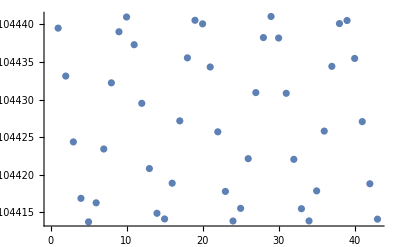

```mathematica
Ξσ2ΠΩI[[3,;;,1,1]]//ListPlot
```

### 8.3 Production and Real Efficiency

```mathematica
χΙ=Compile[Evaluate[ΥΥ],Ι,RuntimeOptions->{"EvaluateSymbolically"->False}];
```

```mathematica
ΞΙ=Table[χΙ@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

```mathematica
ΞE0Ι=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*χΙ@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

```mathematica
ΞE0Ι2=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(χΙ@@ψΞSOLΥ[Πi,θXi,θYi])^2,{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

```mathematica
ΞVar0Ι=Sqrt[ΞE0Ι2-ΞE0Ι^2];
```

```mathematica
ΞE0x=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*ΞEΠΩU[[Πi,θXi,θYi]],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

```mathematica
Do[χϵf[Πi]=(K1-Ι)+ΞΠ[[Πi]]*(K1*(1- δ)+Ι)-(c*Ι^2)/(2*K1),{Πi,NΠ}]
```

```mathematica
Ξχϵf=Table[Compile[Evaluate[ΥΥ],Evaluate[χϵf[Πi]],RuntimeOptions->{"EvaluateSymbolically"->False}],{Πi,NΠ}];
```

```mathematica
ΞE0Ξχϵf=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*Ξχϵf[[Πi]]@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}]-2+δ;
```

```mathematica
ΞE0Ξχϵf
```

0.0063145

```mathematica
ΞE0Ξχϵfo1=(2-δ+(EΠ-1)*(1+(EΠ-1)/(2c))+1/(2c)*ΞPI^2)-(2-δ)
```

0.00667125

```mathematica
ΞE0Ξχϵfo2=(2-δ+(EΠ-1)*(1+(EΠ-1)/(2c))+1/(2c)*ΞPIo^2)-(2-δ)
```

0.00667125

```mathematica
ΞE0Ξχϵfo3=(2-δ+(ΞE0EΠΩU-1)*(1+(ΞE0EΠΩU-1)/(2c))+1/(2c)*ΞPI^2)-(2-δ)
```

0.035121

8.3.1 Conditional Real Efficiency

```mathematica
(*"I" minus (z/kappa)*K1. *)
```

```mathematica
Do[χCϵf[Πi]=Ι-K1*(ΞΠ[[Πi]]-1)/c,{Πi,NΠ}]
```

```mathematica
ΞχCϵf=Table[Compile[Evaluate[ΥΥ],Evaluate[χCϵf[Πi]],RuntimeOptions->{"EvaluateSymbolically"->False}],{Πi,NΠ}];
```

```mathematica
ΞCϵf=Table[ΞχCϵf[[Πi]]@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

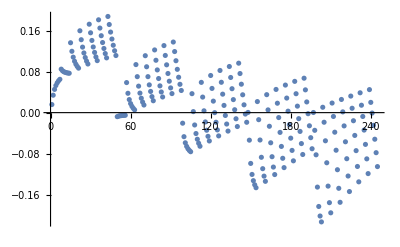

```mathematica
ΞCϵf//Flatten//ListPlot
```

```mathematica
ΞχCϵf2=Table[Compile[Evaluate[ΥΥ],Evaluate[χCϵf[Πi]^2],RuntimeOptions->{"EvaluateSymbolically"->False}],{Πi,NΠ}];
```

```mathematica
ΞCϵf2=Table[ΞχCϵf2[[Πi]]@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

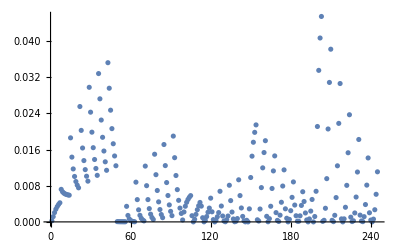

```mathematica
ΞCϵf2//Flatten//ListPlot
```

### 8.4 Asset Prices

```mathematica
χPX=Compile[Evaluate[ΥΥ],PX,RuntimeOptions->{"EvaluateSymbolically"->False}];
χPY=Compile[Evaluate[ΥΥ],PY,RuntimeOptions->{"EvaluateSymbolically"->False}];
```

```mathematica
ΞPX=Table[χPX@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞPY=Table[χPY@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞR=Table[1/(χPY@@ψΞSOLΥ[Πi,θXi,θYi]),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞQ=Table[χPX@@ψΞSOLΥ[Πi,θXi,θYi]/χPY@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

```mathematica
ΞE0PX=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*χPX@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞE0PY=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*χPY@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞE0R=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(1/χPY@@ψΞSOLΥ[Πi,θXi,θYi]),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞE0Q=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(χPX@@ψΞSOLΥ[Πi,θXi,θYi]/χPY@@ψΞSOLΥ[Πi,θXi,θYi]),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

### 8.5 Asset Returns

Unconditional

```mathematica
If[Ui==2,
ΞE0RXΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(ψΩU[Πi,θXi,θYi].((ππ/ΞPX[[Πi,θXi,θYi]]))),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞE0RX2ΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(ψΩU[Πi,θXi,θYi].(((ππ/ΞPX[[Πi,θXi,θYi]]))^2)),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞE0XRXΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(ψΩU[Πi,θXi,θYi].(((ππ/ΞPX[[Πi,θXi,θYi]])-ΞR[[Πi,θXi,θYi]]))),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞE0XRX2ΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(ψΩU[Πi,θXi,θYi].((((ππ/ΞPX[[Πi,θXi,θYi]])-ΞR[[Πi,θXi,θYi]]))^2)),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
,
ΞE0RXΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(ψΩU[Πi,θXi,θYi].((ππ-ΞPX[[Πi,θXi,θYi]]))),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞE0RX2ΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(ψΩU[Πi,θXi,θYi].(((ππ-ΞPX[[Πi,θXi,θYi]]))^2)),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞE0XRXΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(ψΩU[Πi,θXi,θYi].((ππ-ΞPX[[Πi,θXi,θYi]]*ΞR[[Πi,θXi,θYi]]))),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞE0XRX2ΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(ψΩU[Πi,θXi,θYi].(((ππ-ΞPX[[Πi,θXi,θYi]]*ΞR[[Πi,θXi,θYi]]))^2)),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];]
```

```mathematica
ΞS0RXΩU=Sqrt[ΞE0RX2ΩU-ΞE0RXΩU^2];
ΞS0XRXΩU=Sqrt[ΞE0XRX2ΩU-ΞE0XRXΩU^2];
```

Expected Conditional

```mathematica
If[Ui==2,
ΞERXΩU=Table[ψΩU[Πi,θXi,θYi].((ππ/ΞPX[[Πi,θXi,θYi]])),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞERX2ΩU=Table[ψΩU[Πi,θXi,θYi].((ππ/ΞPX[[Πi,θXi,θYi]])^2),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞEXRXΩU=Table[ψΩU[Πi,θXi,θYi].((ππ/ΞPX[[Πi,θXi,θYi]])-ΞR[[Πi,θXi,θYi]]),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞEXRX2ΩU=Table[ψΩU[Πi,θXi,θYi].(((ππ/ΞPX[[Πi,θXi,θYi]])-ΞR[[Πi,θXi,θYi]])^2),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
,
ΞERXΩU=Table[ψΩU[Πi,θXi,θYi].((ππ-ΞPX[[Πi,θXi,θYi]])),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞERX2ΩU=Table[ψΩU[Πi,θXi,θYi].((ππ-ΞPX[[Πi,θXi,θYi]])^2),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞEXRXΩU=Table[ψΩU[Πi,θXi,θYi].((ππ-ΞPX[[Πi,θXi,θYi]]*ΞR[[Πi,θXi,θYi]])),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞEXRX2ΩU=Table[ψΩU[Πi,θXi,θYi].(((ππ-ΞPX[[Πi,θXi,θYi]]*ΞR[[Πi,θXi,θYi]]))^2),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];]
```

```mathematica
ΞSRXΩU=Table[Sqrt[ΞERX2ΩU[[Πi,θXi,θYi]]-ΞERXΩU[[Πi,θXi,θYi]]^2],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞSXRXΩU=Table[Sqrt[ΞEXRX2ΩU[[Πi,θXi,θYi]]-ΞEXRXΩU[[Πi,θXi,θYi]]^2],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

```mathematica
ΞE0ERXΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*ΞERXΩU[[Πi,θXi,θYi]],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];ΞE0EXRXΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*ΞEXRXΩU[[Πi,θXi,θYi]],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞE0ESRXΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*ΞSRXΩU[[Πi,θXi,θYi]],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
ΞE0ESXRXΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*ΞSXRXΩU[[Πi,θXi,θYi]],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

### 8.6 Asset Demand

```mathematica
χX=Compile[Evaluate[ΥΥ],Evaluate[Table[X[πi],{πi,Nπ}]],RuntimeOptions->{"EvaluateSymbolically"->False}];
χY=Compile[Evaluate[ΥΥ],Evaluate[Table[Y[πi],{πi,Nπ}]],RuntimeOptions->{"EvaluateSymbolically"->False}];
```

```mathematica
ΞX=Table[(χX@@ψΞSOLΥ[Πi,θXi,θYi])[[Si]],{Πi,NΠ},{Si,NS},{θXi,NθX},{θYi,NθY}];
```

```mathematica
χXΣ=Compile[Evaluate[ΥΥ],Evaluate[Table[XΣ[πi],{πi,Nπ}]],RuntimeOptions->{"EvaluateSymbolically"->False}];
χYΣ=Compile[Evaluate[ΥΥ],Evaluate[Table[YΣ[πi],{πi,Nπ}]],RuntimeOptions->{"EvaluateSymbolically"->False}];
```

### 8.7 Consumption

```mathematica
χC1=Compile[Evaluate[ΥΥ],Evaluate[Table[Evaluate[C1[Si]],{Si,NS}]],RuntimeOptions->{"EvaluateSymbolically"->False}];
ΞC1=Table[χC1@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

```mathematica
ΞE0C1ΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(SΩπ[[ΞΠi[[Πi]],;;]].χC1@@ψΞSOLΥ[Πi,θXi,θYi]),{Πi,NΠ},{θXi,NθX},{θYi,NθY}]/.τϵi->τϵ0
```

0.

```mathematica
EC2[Si]=Evaluate[Sum[(ΩΩI[πi,Si]/ΣΩI[Si])*C2[πi,Si],{πi,Nπ}]]/.τϵi->τϵ0;
EC22[Si]=Evaluate[Sum[(ΩΩI[πi,Si]/ΣΩI[Si])*C2[πi,Si]^2,{πi,Nπ}]]/.τϵi->τϵ0;
SC2[Si]=Sqrt[Max[0,EC22[Si]-(EC2[Si]^2)]]/.τϵi->τϵ0;
```

```mathematica
ΞEC2=Table[Evaluate[EC2[Si]]/.Si->Six/.RΩΩI/.RΣΩI,{Six,NS}]/.τϵi->τϵ0;
ΞSC2=Table[Evaluate[SC2[Si]]/.Si->Six/.RΩΩI/.RΣΩI,{Six,NS}]/.τϵi->τϵ0;
χΞEC2=Compile[Evaluate[ΥΥ],Evaluate[ΞEC2],RuntimeOptions->{"EvaluateSymbolically"->False}]/.τϵi->τϵ0;χΞSC2=Compile[Evaluate[ΥΥ],Evaluate[ΞSC2],RuntimeOptions->{"EvaluateSymbolically"->False}]/.τϵi->τϵ0;
```

```mathematica
ΞΞEC2=Table[χΞEC2@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

```mathematica
ΞE0C2ΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(SΩπ[[ΞΠi[[Πi]],;;]].χΞEC2@@ψΞSOLΥ[Πi,θXi,θYi]),{Πi,NΠ},{θXi,NθX},{θYi,NθY}]/.τϵi->τϵ0;
```

```mathematica
ΞE0σC2ΩU=Sum[ΞΠXnYnΩ[[Πi,θXi,θYi]]*(SΩπ[[ΞΠi[[Πi]],;;]].χΞSC2@@ψΞSOLΥ[Πi,θXi,θYi]),{Πi,NΠ},{θXi,NθX},{θYi,NθY}]/.τϵi->τϵ0
```

0.292155

### 8.8 Aggregate Consumption

```mathematica
ΞχΣC1=Table[Compile[Evaluate[ΥΥ],Evaluate[ΣC1[Πi]],RuntimeOptions->{"EvaluateSymbolically"->False}],{Πi,NΠ}];
```

```mathematica
ΞΣC1=Table[ΞχΣC1[[Πi]]@@ψΞSOLΥ[Πi,θXi,θYi],{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

### 8.A: Compare Q-Model

```mathematica
ΞRrefQ=Table[(θYbar-ΞθY[[θYi]])/(ΣW00-(θXbar-ΞθX[[θXi]])*ΞPX[[Πi,θXi,θYi]]),{Πi,NΠ},{θXi,NθX},{θYi,NθY}];
```

```mathematica
ErrorRefQ=Max[Abs[ΞRrefQ-ΞR]]
```

8.88178×10^-16

```mathematica
ΞXrefQ=Table[(ΞEΠΩI[[Πi,Si,θXi,θYi]]-ΞQ[[Πi,θXi,θYi]])/(γ*Ξσ2ΠΩI[[Πi,Si,θXi,θYi]]),{Πi,NΠ},{Si,NS},{θXi,NθX},{θYi,NθY}];
```

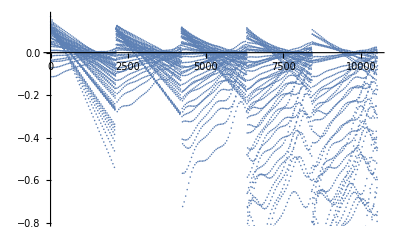

```mathematica
Flatten[ΞXrefQ-ΞX]//ListPlot
```

## Graphs B: Conditional (Scatter) Plots

### B.0 Graphic Options

```mathematica
Asize=200;
```

```mathematica
ΞColor={GrayLevel[0.5],RGBColor[1, Rational[5, 9], Rational[5, 9]],RGBColor[Rational[5, 9], Rational[5, 9], 1],RGBColor[Rational[5, 9], 1, Rational[5, 9]],RGBColor[1, 1, Rational[1, 3]],RGBColor[0, 1, 1],RGBColor[1, 0.6666666666666666, Rational[1, 3]],,,,RGBColor[0.44444444444444453, 0.44444444444444453, 0.44444444444444453],RGBColor[Rational[4, 9], Rational[20, 81], Rational[20, 81]],RGBColor[Rational[20, 81], Rational[20, 81], Rational[4, 9]],RGBColor[Rational[20, 81], Rational[4, 9], Rational[20, 81]],RGBColor[Rational[4, 9], Rational[4, 9], Rational[4, 27]],RGBColor[0, Rational[4, 9], Rational[4, 9]],RGBColor[Rational[4, 9], 0.2962962962962963, Rational[4, 27]],,,,};
```

```mathematica
ΓA=Function[{datax,datay,xlabel,ylabel,colori},ListLinePlot[Transpose[{datax,datay}],Frame->{{True,False},{True,False}},PlotLabel->ylabel,FrameLabel->{{Null,Null},{xlabel,Null}},PlotStyle->ΞColor[[colori]],ImageSize->Asize,AspectRatio->1.1,ImagePadding->{{40,00},{45,00}},LabelStyle->{FontSize->9,FontFamily->"Helvetica"},AxesStyle->{FontSize->9}]];
```

### B.1 Price Informativeness

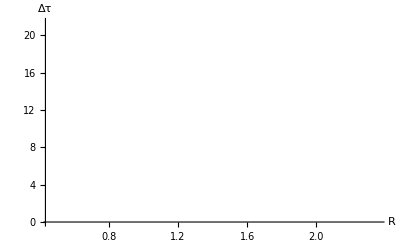

```mathematica
ListPlot[Transpose[{Flatten[ΞR],Flatten[ΞτΔΠΩU]}],AxesLabel->{"R","Δτ"},PlotStyle->White]
```

```mathematica
Transpose[{Flatten[ΞR],Flatten[ΞτΔΠΩU]}]//VEC
```

((0.5796, 2.61)(0.5882, 2.308)(0.5777, 2.156)(0.5562, 2.07)(0.5281, 2.016)(0.4958, 1.979)(0.4608, 1.954)(0.8365, 1.841)(0.7812, 1.847)(0.7308, 1.851)(0.6827, 1.854)(0.6357, 1.857)(0.5894, 1.859)(0.5436, 1.86)(1.059, 2.412)(0.9494, 2.143)(0.8629, 2.018)(0.7905, 1.957)(0.7265, 1.926)(0.6677, 1.908)(0.6124, 1.899)(1.167, 3.46)(1.053, 2.905)(0.954, 2.553)(0.8691, 2.338)(0.7944, 2.205)(0.727, 2.121)(0.6647, 2.065)(1.204, 4.503)(1.098, 3.796)(1.002, 3.27)(0.9151, 2.9)(0.8368, 2.644)(0.7653, 2.468)(0.6993, 2.345)(1.198, 5.478)(1.104, 4.691)(1.014, 4.051)(0.9313, 3.556)(0.8542, 3.187)(0.7827, 2.915)(0.7159, 2.715)(1.165, 6.384)(1.08, 5.559)(0.9994, 4.843)(0.9223, 4.254)(0.8493, 3.789)(0.7804, 3.429)(0.7152, 3.153)(0.7868, 1.88)(0.746, 1.874)(0.7036, 1.872)(0.6605, 1.87)(0.617, 1.869)(0.5732, 1.868)(0.5293, 1.867)(1.087, 2.384)(0.9524, 2.073)(0.8595, 1.964)(0.7856, 1.918)(0.7216, 1.897)(0.6631, 1.887)(0.6081, 1.882)(1.269, 3.867)(1.115, 3.035)(0.9909, 2.563)(0.8922, 2.309)(0.8101, 2.168)(0.7384, 2.085)(0.6736, 2.034)(1.336, 5.255)(1.197, 4.229)(1.073, 3.477)(0.9666, 2.979)(0.8748, 2.661)(0.7946, 2.457)(0.7227, 2.323)(1.342, 6.475)(1.221, 5.382)(1.108, 4.486)(1.005, 3.802)(0.9118, 3.313)(0.8287, 2.972)(0.7535, 2.734)(1.312, 7.575)(1.207, 6.447)(1.105, 5.487)(1.01, 4.683)(0.9215, 4.056)(0.8402, 3.586)(0.7653, 3.24)(1.255, 8.615)(1.164, 7.419)(1.075, 6.443)(0.9886, 5.574)(0.907, 4.841)(0.8303, 4.261)(0.7584, 3.814)(1.105, 2.326)(0.9401, 1.989)(0.8459, 1.911)(0.7737, 1.885)(0.7113, 1.874)(0.6541, 1.87)(0.6003, 1.869)(1.439, 4.771)(1.202, 3.298)(1.03, 2.578)(0.9119, 2.271)(0.8214, 2.125)(0.7458, 2.047)(0.6788, 2.002)(1.538, 6.703)(1.345, 5.054)(1.171, 3.851)(1.028, 3.106)(0.9156, 2.685)(0.8235, 2.444)(0.7446, 2.298)(1.55, 8.316)(1.392, 6.597)(1.239, 5.244)(1.101, 4.215)(0.9815, 3.508)(0.8805, 3.053)(0.7935, 2.759)(1.518, 9.767)(1.384, 7.975)(1.253, 6.539)(1.127, 5.388)(1.013, 4.479)(0.9119, 3.82)(0.8223, 3.362)(1.456, 11.04)(1.34, 9.301)(1.227, 7.714)(1.117, 6.517)(1.013, 5.502)(0.9168, 4.683)(0.8294, 4.071)(1.371, 12.05)(1.272, 10.62)(1.173, 8.841)(1.078, 7.555)(0.985, 6.515)(0.8972, 5.593)(0.8152, 4.847)(1.776, 7.25)(1.375, 4.099)(1.074, 2.608)(0.9257, 2.22)(0.8268, 2.076)(0.7482, 2.007)(0.68, 1.97)(1.865, 9.448)(1.607, 6.987)(1.334, 4.708)(1.112, 3.346)(0.9607, 2.723)(0.8516, 2.428)(0.7643, 2.268)(1.867, 10.88)(1.661, 9.077)(1.452, 6.798)(1.247, 5.031)(1.075, 3.855)(0.942, 3.178)(0.8369, 2.794)(1.816, 12.04)(1.65, 10.65)(1.475, 8.62)(1.305, 6.683)(1.144, 5.245)(1.006, 4.214)(0.8908, 3.549)(1.733, 13.36)(1.596, 11.68)(1.45, 10.3)(1.304, 8.192)(1.164, 6.627)(1.034, 5.403)(0.9196, 4.482)(1.631, 15.08)(1.512, 12.41)(1.391, 11.67)(1.265, 9.705)(1.144, 7.894)(1.028, 6.608)(0.921, 5.523)(1.512, 17.25)(1.406, 13.21)(1.304, 12.55)(1.199, 11.24)(1.093, 9.134)(0.9923, 7.726)(0.8961, 6.6)(2.356, 15.26)(2.081, 10.81)(1.711, 7.578)(1.267, 4.029)(1.014, 2.791)(0.8781, 2.406)(0.7808, 2.233)(2.318, 17.12)(2.084, 13.13)(1.829, 10.13)(1.53, 7.187)(1.232, 4.668)(1.023, 3.406)(0.8855, 2.847)(2.245, 17.57)(2.034, 15.8)(1.835, 11.64)(1.605, 9.665)(1.369, 6.94)(1.15, 5.023)(0.9814, 3.876)(2.131, 17.05)(1.96, 18.51)(1.781, 13.24)(1.604, 11.31)(1.408, 9.047)(1.219, 6.807)(1.05, 5.257)(1.991, 16.48)(1.858, 20.13)(1.698, 15.54)(1.549, 12.23)(1.391, 11.01)(1.229, 8.488)(1.077, 6.746)(1.836, 16.35)(1.726, 20.16)(1.596, 18.52)(1.461, 13.21)(1.333, 12.32)(1.196, 10.28)(1.064, 8.129)(1.673, 16.86)(1.574, 19.25)(1.471, 21.37)(1.354, 14.82)(1.242, 12.93)(1.131, 12.05)(1.017, 9.532))

### B.2 Quantities against uB / Rf

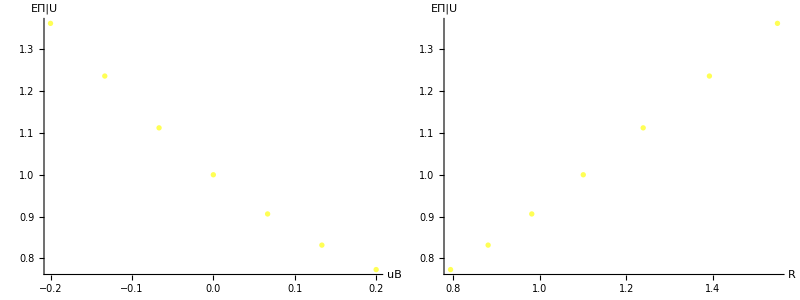

```mathematica
(* i *)Grid[{{ListPlot[Transpose[{ΞθY,ΞEΠΩU[[μΠi,μθXi,;;]]}],AxesLabel->{"uB","EΠ|U"},PlotStyle->ΞColor[[5]],ImageSize->300],ListPlot[Transpose[{ΞR[[μΠi,μθXi,;;]],ΞEΠΩU[[μΠi,μθXi,;;]]}],PlotStyle->ΞColor[[5]],ImageSize->300,AxesLabel->{"R","EΠ|U"}]}}]
```

```mathematica
Transpose[{ΞθY,ΞEΠΩU[[μΠi,μθXi,;;]]}]//VEC
```

((-0.2, 1.362)(-0.1333, 1.236)(-0.06667, 1.112)(0., 1.)(0.06667, 0.9062)(0.1333, 0.8316)(0.2, 0.7731))

```mathematica
(* ii *)
```

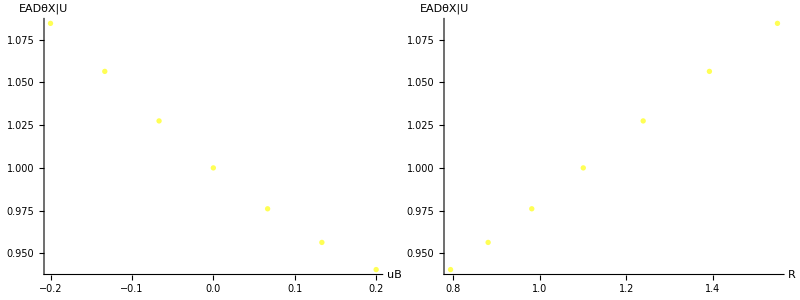

```mathematica
Grid[{{ListPlot[Transpose[{ΞθY,ΞEADXΩU[[μΠi,μθXi,;;]]}],AxesLabel->{"uB","EADθX|U"},PlotStyle->ΞColor[[5]],ImageSize->300],ListPlot[Transpose[{ΞR[[μΠi,μθXi,;;]],ΞEADXΩU[[μΠi,μθXi,;;]]}],PlotStyle->ΞColor[[5]],ImageSize->300,AxesLabel->{"R","EADθX|U"}]}}]
```

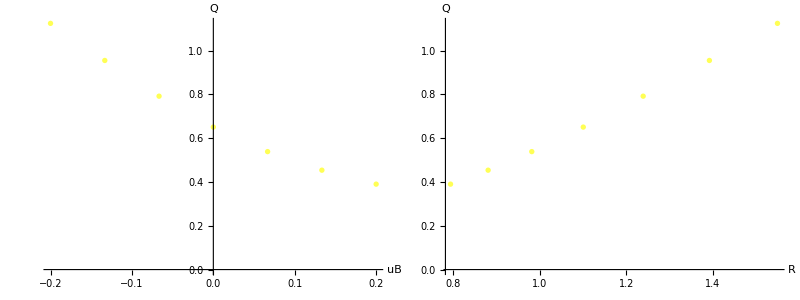

```mathematica
(* iii *)Grid[{{ListPlot[Transpose[{ΞθY,ΞQ[[μΠi,μθXi,;;]]}],AxesLabel->{"uB","Q"},PlotStyle->ΞColor[[5]],ImageSize->300],ListPlot[Transpose[{ΞR[[μΠi,μθXi,;;]],ΞQ[[μΠi,μθXi,;;]]}],PlotStyle->ΞColor[[5]],ImageSize->300,AxesLabel->{"R","Q"}]}}]
```

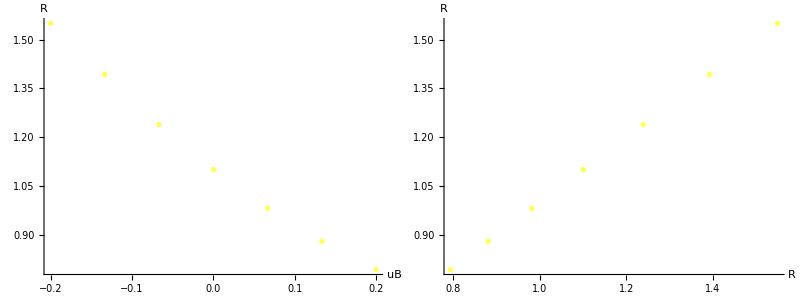

```mathematica
(* iv *)Grid[{{ListPlot[Transpose[{ΞθY,ΞR[[μΠi,μθXi,;;]]}],AxesLabel->{"uB","R"},PlotStyle->ΞColor[[5]],ImageSize->300],ListPlot[Transpose[{ΞR[[μΠi,μθXi,;;]],ΞR[[μΠi,μθXi,;;]]}],PlotStyle->ΞColor[[5]],ImageSize->300,AxesLabel->{"R","R"}]}}]
```

```mathematica
Transpose[{ΞθY,ΞR[[μΠi,μθXi,;;]]}]//VEC
```

((-0.2, 1.55)(-0.1333, 1.392)(-0.06667, 1.239)(0., 1.101)(0.06667, 0.9815)(0.1333, 0.8805)(0.2, 0.7935))

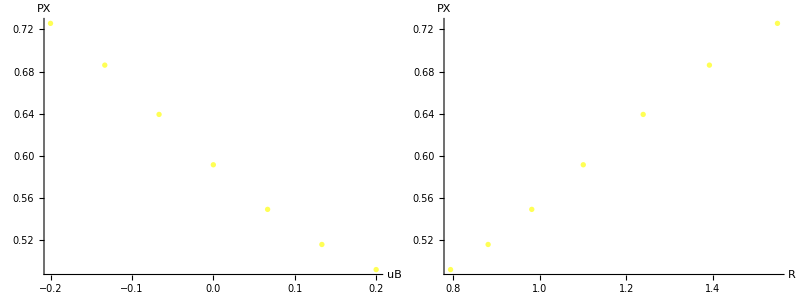

```mathematica
(* v *)Grid[{{ListPlot[Transpose[{ΞθY,ΞPX[[μΠi,μθXi,;;]]}],AxesLabel->{"uB","PX"},PlotStyle->ΞColor[[5]],ImageSize->300],ListPlot[Transpose[{ΞR[[μΠi,μθXi,;;]],ΞPX[[μΠi,μθXi,;;]]}],PlotStyle->ΞColor[[5]],ImageSize->300,AxesLabel->{"R","PX"}]}}]
```

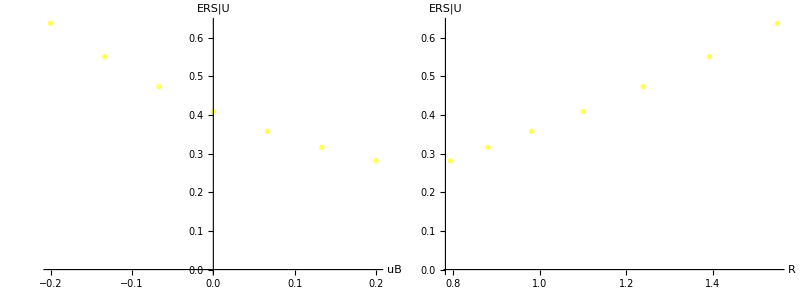

```mathematica
(* vi.a*)Grid[{{ListPlot[Transpose[{ΞθY,ΞERXΩU[[μΠi,μθXi,;;]]}],AxesLabel->{"uB","ERS|U"},PlotStyle->ΞColor[[5]],ImageSize->300],ListPlot[Transpose[{ΞR[[μΠi,μθXi,;;]],ΞERXΩU[[μΠi,μθXi,;;]]}],PlotStyle->ΞColor[[5]],ImageSize->300,AxesLabel->{"R","ERS|U"}]}}]
```

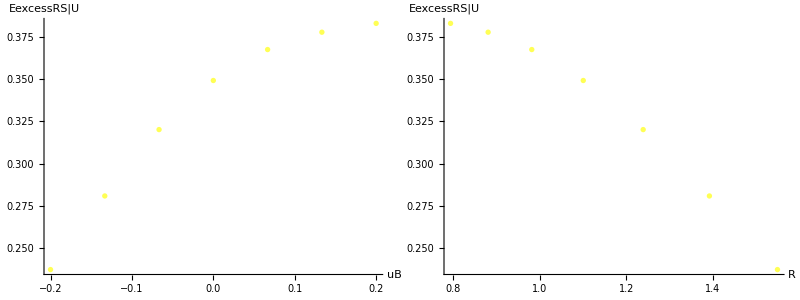

```mathematica
(* vi.b*)Grid[{{ListPlot[Transpose[{ΞθY,ΞEXRXΩU[[μΠi,μθXi,;;]]}],AxesLabel->{"uB","EexcessRS|U"},PlotStyle->ΞColor[[5]],ImageSize->300],ListPlot[Transpose[{ΞR[[μΠi,μθXi,;;]],ΞEXRXΩU[[μΠi,μθXi,;;]]}],PlotStyle->ΞColor[[5]],ImageSize->300,AxesLabel->{"R","EexcessRS|U"}]}}]
```

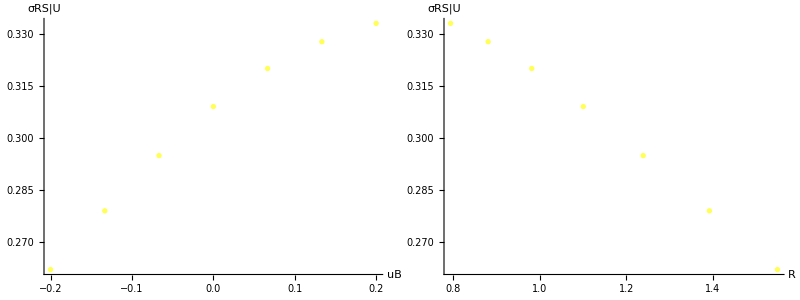

```mathematica
(* vii *)Grid[{{ListPlot[Transpose[{ΞθY,ΞSRXΩU[[μΠi,μθXi,;;]]}],AxesLabel->{"uB","σRS|U"},PlotStyle->ΞColor[[5]],ImageSize->300],ListPlot[Transpose[{ΞR[[μΠi,μθXi,;;]],ΞSRXΩU[[μΠi,μθXi,;;]]}],PlotStyle->ΞColor[[5]],ImageSize->300,AxesLabel->{"R","σRS|U"}]}}]
```

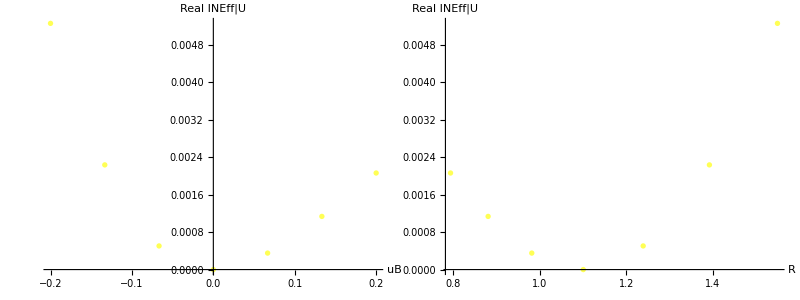

```mathematica
(* viii *)Grid[{{ListPlot[Transpose[{ΞθY,ΞCϵf2[[μΠi,μθXi,;;]]}],AxesLabel->{"uB","Real INEff|U"},PlotStyle->ΞColor[[5]],ImageSize->300],ListPlot[Transpose[{ΞR[[μΠi,μθXi,;;]],ΞCϵf2[[μΠi,μθXi,;;]]}],PlotStyle->ΞColor[[5]],ImageSize->300,AxesLabel->{"R","Real INEff|U"}]}}]
```

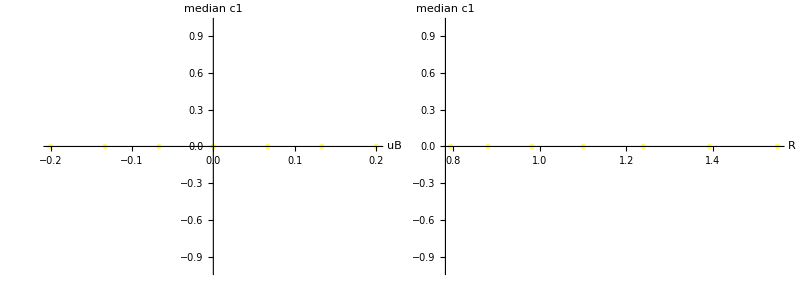

```mathematica
(* ix *)Grid[{{ListPlot[Transpose[{ΞθY,ΞC1[[μΠi,μθXi,;;,μSi]]}],AxesLabel->{"uB","median c1"},PlotStyle->ΞColor[[5]],ImageSize->300],ListPlot[Transpose[{ΞR[[μΠi,μθXi,;;]],ΞC1[[μΠi,μθXi,;;,μSi]]}],PlotStyle->ΞColor[[5]],ImageSize->300,AxesLabel->{"R","median c1"}]}}]
```

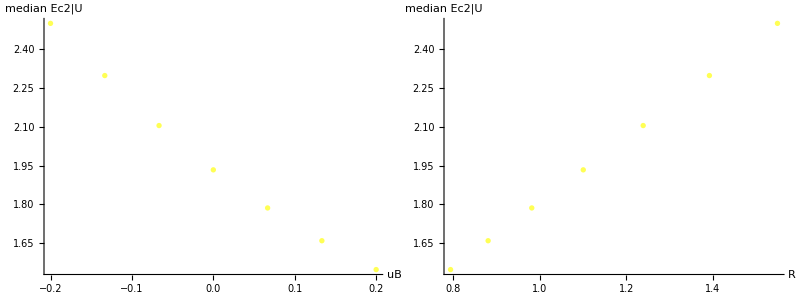

```mathematica
(* x *)Grid[{{ListPlot[Transpose[{ΞθY,ΞΞEC2[[μΠi,μθXi,;;,μSi]]}],AxesLabel->{"uB","median Ec2|U"},PlotStyle->ΞColor[[5]],ImageSize->300],ListPlot[Transpose[{ΞR[[μΠi,μθXi,;;]],ΞΞEC2[[μΠi,μθXi,;;,μSi]]}],PlotStyle->ΞColor[[5]],ImageSize->300,AxesLabel->{"R","median Ec2|U"}]}}]
```

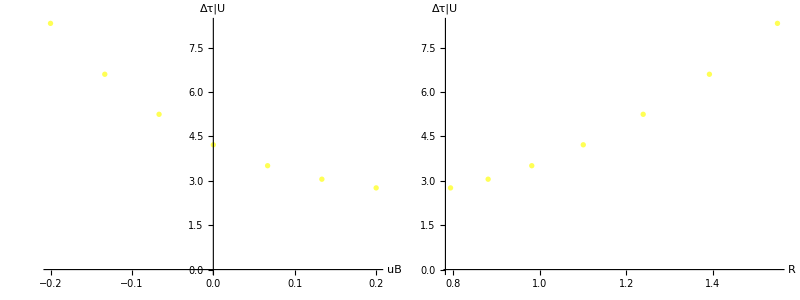

```mathematica
(* xi *)Grid[{{ListPlot[Transpose[{ΞθY,ΞτΔΠΩU[[μΠi,μθXi,;;]]}],AxesLabel->{"uB","Δτ|U"},PlotStyle->ΞColor[[5]],ImageSize->300],ListPlot[Transpose[{ΞR[[μΠi,μθXi,;;]],ΞτΔΠΩU[[μΠi,μθXi,;;]]}],PlotStyle->ΞColor[[5]],ImageSize->300,AxesLabel->{"R","Δτ|U"}]}}]
```

```mathematica
Transpose[{ΞθY,ΞτΔΠΩU[[μΠi,μθXi,;;]]}]//VEC
```

((-0.2, 8.316)(-0.1333, 6.597)(-0.06667, 5.244)(0., 4.215)(0.06667, 3.508)(0.1333, 3.053)(0.2, 2.759))

### B.3 ER/EXR/CVol/RE vs Rf

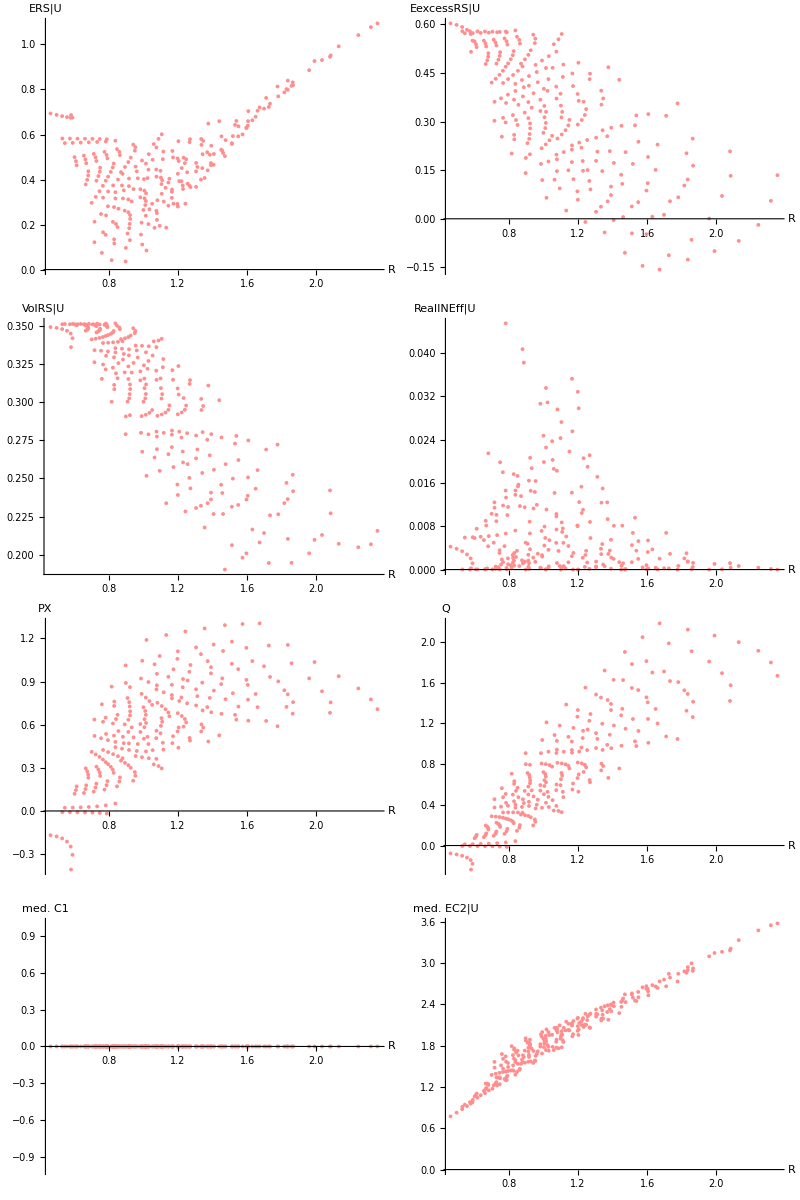

```mathematica
Grid[{{ListPlot[Transpose[{Flatten[ΞR],Flatten[ΞERXΩU]}],AxesLabel->{"R","ERS|U"},PlotStyle->ΞColor[[2]],ImageSize->300],ListPlot[Transpose[{Flatten[ΞR],Flatten[ΞEXRXΩU]}],AxesLabel->{"R","EexcessRS|U"},PlotStyle->ΞColor[[2]],ImageSize->300]},{ListPlot[Transpose[{Flatten[ΞR],Flatten[ΞSRXΩU]}],AxesLabel->{"R","VolRS|U"},PlotStyle->ΞColor[[2]],ImageSize->300],ListPlot[Transpose[{Flatten[ΞR],Flatten[ΞCϵf2]}],AxesLabel->{"R","RealINEff|U"},PlotStyle->ΞColor[[2]],ImageSize->300]},{ListPlot[Transpose[{Flatten[ΞR],Flatten[ΞPX]}],AxesLabel->{"R","PX"},PlotStyle->ΞColor[[2]],ImageSize->300],ListPlot[Transpose[{Flatten[ΞR],Flatten[ΞQ[[;;,;;,;;]]]}],AxesLabel->{"R","Q"},PlotStyle->ΞColor[[2]],ImageSize->300]},{ListPlot[Transpose[{Flatten[ΞR],Flatten[ΞC1[[;;,;;,;;,μSi]]]}],AxesLabel->{"R","med. C1"},PlotStyle->ΞColor[[2]],ImageSize->300],ListPlot[Transpose[{Flatten[ΞR],Flatten[ΞΞEC2[[;;,;;,;;,μSi]]]}],AxesLabel->{"R","med. EC2|U"},PlotStyle->ΞColor[[2]],ImageSize->300]}}]
```

```mathematica
Correlation[WeightedData[Flatten[ΞR],Flatten[ΞΠXnYnΩ]],WeightedData[Flatten[ΞCϵf2],Flatten[ΞΠXnYnΩ]]]//Chop
```

-0.134333